# Curves

## In plane

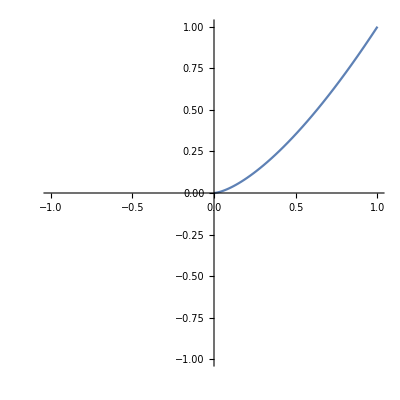

```mathematica
ParametricPlot[{t^2,t^3},{t,0,1},PlotRange->{{-1,1},{-1,1}}]
```

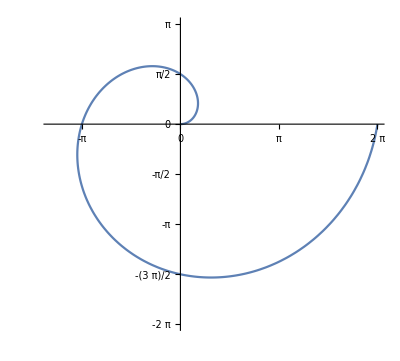

```mathematica
ParametricPlot[{t Cos[t],t Sin[t]},{t,0,2π},PlotRange->{{-π-1,2π},{-2π,π}},Ticks->{Range[-π,2π,π/2],Range[-2π,3 π/2,π/2]}]
```

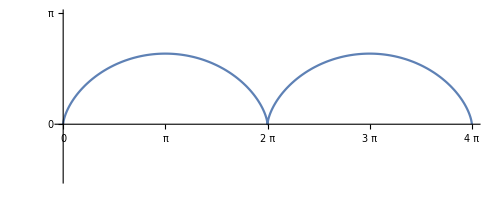

```mathematica
ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,4π},PlotRange->{{0,4π},{-π/2,π}},Ticks->{Range[-π,4π,π/2],Range[-2π,3 π/2,π/2]}]
```

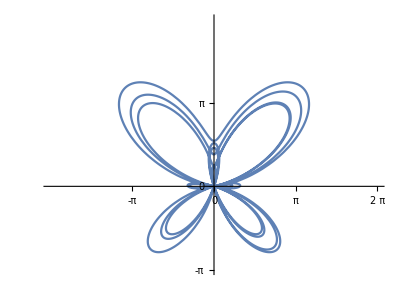

```mathematica
ParametricPlot[{Sin[t](ⅇ^Cos[t]-2Cos[4t]+Sin[t/12]^5),Cos[t](ⅇ^Cos[t]-2Cos[4t]+Sin[t/12]^5)},{t,0,7π},PlotRange->{{-2π,2π},{-π,2π}},Ticks->{Range[-π,2π,π/2],Range[-2π,3 π/2,π/2]}]
```

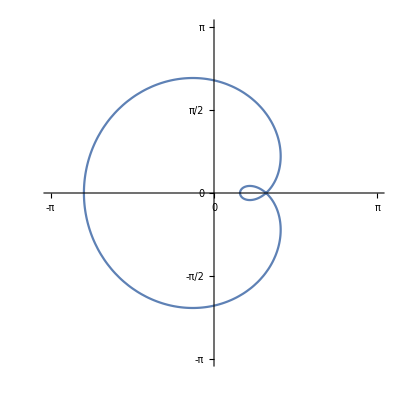

```mathematica
ParametricPlot[{1.5Cos[t]-Cos[2t],1.5Sin[t]-Sin[2t]},{t,0,2π},PlotRange->{{-π,π},{-π,π}},Ticks->{Range[-π,2π,π/2],Range[-2π,3 π/2,π/2]}]
```

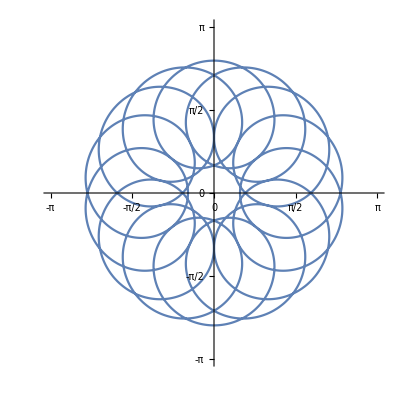

```mathematica
ParametricPlot[{1.5Cos[t]-Cos[15t],1.5Sin[t]-Sin[15t]},{t,0,2π},PlotRange->{{-π,π},{-π,π}},Ticks->{Range[-π,π,π/2],Range[-π,π,π/2]}]
```

```mathematica
Manipulate[ParametricPlot[{1.5Cos[t]-Cos[p t],1.5Sin[t]-Sin[p t]},{t,0,2π},PlotRange->{{-π,π},{-π,π}},Ticks->{Range[-π,π,π/2],Range[-π,π,π/2]}],{p,{2,5,7,10,15,20,50}}]
```

```mathematica
Manipulate[ParametricPlot[{1.5Cos[t]-Cos[5 t],1.5Sin[t]-Sin[p t]},{t,0,2π},PlotRange->{{-π,π},{-π,π}},Ticks->{Range[-π,π,π/2],Range[-π,π,π/2]}],{p,{2,4,6,7,8,9,13}}]
```

```mathematica
Manipulate[Plot[Sin[x+t],{x,0,2π}],{t,0,2π}(*indice del manipulate{que, de dnde a donde}*)]
```

## In space

```mathematica
ParametricPlot3D[{π Cos[t],π Sin[t],t},{t,0,2π},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{ Cos[t], Sin[t],1},{t,0,2π},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],-Sin[t]},{t,0,2π},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t](ⅇ^Cos[t]-2Cos[4t]+Sin[t/12]^5),Cos[t](ⅇ^Cos[t]-2Cos[4t]+Sin[t/12]^5),Sin[t]},{t,0,2π},PlotRange->{{-2π,2π},{-π,2π}},Ticks->{Range[-π,2π,π/2],Range[-2π,3 π/2,π/2]},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{ t Cos[t], t Sin[t],t},{t,0,7π},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

# Vector Fields

## 2D

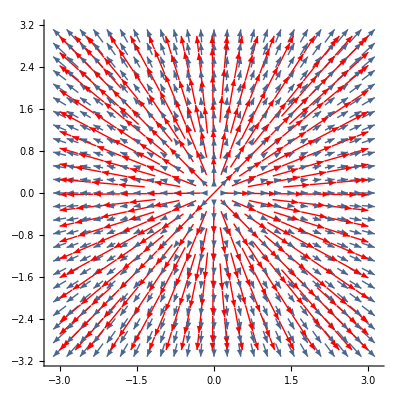

```mathematica
VectorPlot[{x,y},{x,-3,3},{y,-3,3},VectorStyle->Arrowheads[.01],Frame->False,VectorPoints->Fine,StreamStyle->Red,StreamPoints->80,Axes->True]
```

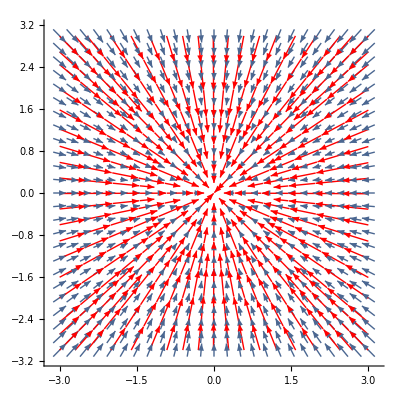

```mathematica
VectorPlot[{-x,-y},{x,-3,3},{y,-3,3},VectorStyle->Arrowheads[.01],Frame->False,VectorPoints->Fine,StreamStyle->Red,StreamPoints->80,Axes->True]
```

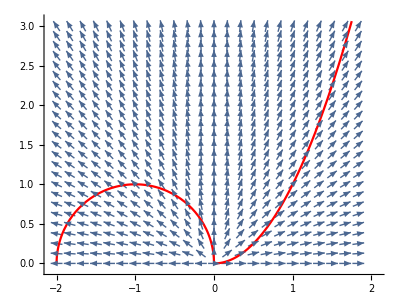

```mathematica
a1=VectorPlot[{x/(√(x^2+y^2)),y/(√(x^2+y^2))},{x,-2,2},{y,0,3},VectorStyle->Arrowheads[.01],VectorScale->{.03,.03},Frame->False,VectorPoints->Fine,Axes->True];
a2=ParametricPlot[{t,t^2},{t,0,1.75},PlotStyle->Red];
a3=ParametricPlot[{Cos[t]-1,Sin[t]},{t,0,π},PlotStyle->Red];
Show[a1,a2,a3,AspectRatio->3/4]
```

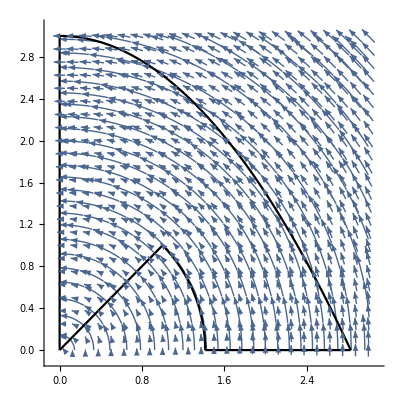

```mathematica
b1=VectorPlot[{-y,x},{x,0,3},{y,0,3},VectorStyle->Arrowheads[.01],Frame->False,VectorPoints->Fine,StreamPoints->60,Axes->True];
b2=ParametricPlot[{t,t},{t,0,1},PlotStyle->Black];
b3=ParametricPlot[{√2 Sin[t],√2 Cos[t]},{t,π/4,π/2},PlotStyle->Black];
b4=ParametricPlot[{t+√2,0},{t,0,√2},PlotStyle->Black];
b5=ParametricPlot[{t,-3/8 t^2+3},{t,0,2 √2},PlotStyle->Black];
b6=ParametricPlot[{0,t},{t,3,0},PlotStyle->Black];
Show[b1,b2,b3,b4,b5,b6,AspectRatio->1]
```

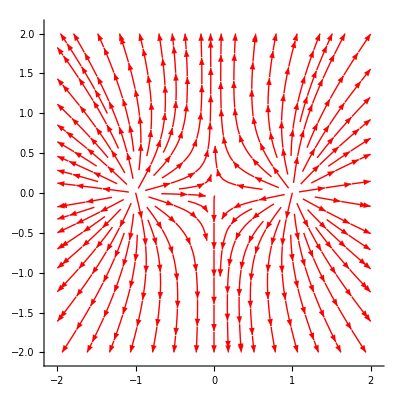

```mathematica
VectorPlot[{(x-1)/(((x-1)^2+y^2)^(3/2))+(x+1)/(((x+1)^2+y^2)^(3/2)),y/(((x-1)^2+y^2)^(3/2))+y/(((x+1)^2+y^2)^(3/2))},{x,-2,2},{y,-2,2},VectorScale->{.02,.02},VectorStyle->Arrowheads[.02],Frame->False,VectorPoints->None,StreamStyle->Red,StreamPoints->80,Axes->True]
```

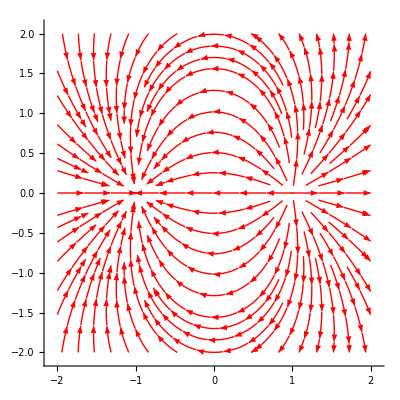

```mathematica
VectorPlot[{(x-1)/(((x-1)^2+y^2)^(3/2))-(x+1)/(((x+1)^2+y^2)^(3/2)),y/(((x-1)^2+y^2)^(3/2))-y/(((x+1)^2+y^2)^(3/2))},{x,-2,2},{y,-2,2},VectorScale->{.02,.02},VectorStyle->Arrowheads[.02],Frame->False,VectorPoints->None,StreamStyle->Red,StreamPoints->80,Axes->True]
```

```mathematica
Manipulate[VectorPlot[{-a(x-1)/(((x-1)^2+y^2)^(3/2))+b(x+1)/(((x+1)^2+y^2)^(3/2)),-a y/(((x-1)^2+y^2)^(3/2))+b y/(((x+1)^2+y^2)^(3/2))},{x,-i,i},{y,-i,i},VectorScale->{.02,.02},VectorStyle->Arrowheads[.02],Frame->False,VectorPoints->None,StreamStyle->Red,StreamPoints->100,Axes->True],{{a,1,"Carga -"},Range[5]},{{b,1,"Carga +"},Range[5]},{{i,3,"Intervalo"},Range[10]}]
```

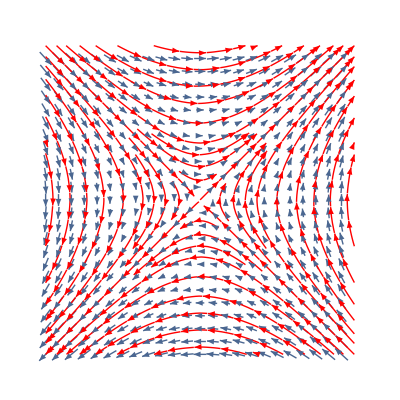

```mathematica
VectorPlot[Evaluate[D[x y,{{x,y}}]],{x,-1,1},{y,-1,1},VectorStyle->Arrowheads[.01],Frame->False,VectorPoints->Fine,StreamStyle->Red,StreamPoints->80](*Forma para dibujar el gradiente*)
```

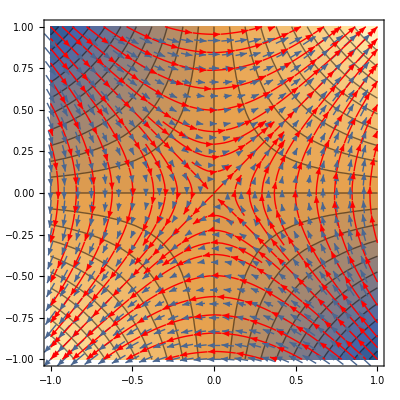

```mathematica
Show[ContourPlot[x y,{x,-1,1},{y,-1,1},Contours->20],VectorPlot[Evaluate[D[x y,{{x,y}}]],{x,-1,1},{y,-1,1},VectorStyle->Arrowheads[.01],Frame->False,VectorPoints->Fine,StreamStyle->Red,StreamPoints->80]]
```

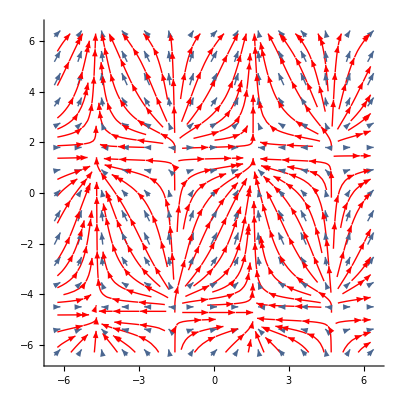

```mathematica
VectorPlot[{Cos[x],1-Sin[y]},{x,-2π,2π},{y,-2π,2π},VectorScale->{.03,.03},VectorStyle->Arrowheads[.015],Frame->False,StreamStyle->Red,StreamPoints->220,Axes->True]
```

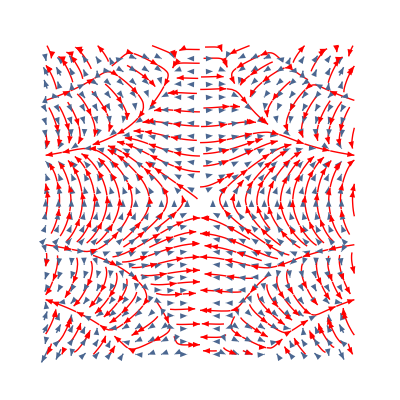

```mathematica
VectorPlot[Evaluate[D[x^2 y Cos[x y^2],{{x,y}}]],{x,-2,2},{y,-2,2},VectorStyle->Arrowheads[.01],Frame->False,VectorPoints->Fine,StreamStyle->Red,StreamPoints->280]
```

## 3D

```mathematica
VectorPlot3D[{x/(√(x^2+y^2+z^2)),y/(√(x^2+y^2+z^2)),z/(√(x^2+y^2+z^2))},{x,-3,3},{y,-3,3},{z,-3,3},VectorPoints->6,Boxed->False,VectorStyle->Arrowheads[0.02],Axes->Automatic,VectorPoints->Fine,VectorScale->{.1,.1},AxesOrigin->{0,0,0},PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
VectorPlot3D[{-y/(√(x^2+y^2)),x/(√(x^2+y^2)),0},{x,-3,3},{y,-3,3},{z,-3,3},VectorPoints->6,Boxed->False,VectorStyle->Arrowheads[0.02],Axes->Automatic,AxesOrigin->{0,0,0},VectorScale->{.1,.1},VectorPoints->Fine,AxesLabel->{x,y,z},PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
VectorPlot3D[{x/(√(x^2+y^2+z^2)),y/(√(x^2+y^2+z^2)),z/(√(x^2+y^2+z^2))},{x,-3,3},{y,-3,3},{z,-3,3},VectorPoints->6,Boxed->False,VectorStyle->Arrowheads[0.02],Axes->Automatic,VectorPoints->Fine,VectorScale->{.1,.1},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
VectorPlot3D[{ⅇ^x,x ⅇ^(x y),x y ⅇ^(x y z)},{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->10,Boxed->False,VectorStyle->Arrowheads[0.015],Axes->Automatic,VectorPoints->Fine,VectorScale->{.1,.1},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
VectorPlot3D[Evaluate[D[x y z,{{x,y,z}}]],{x,-1,1},{y,-1,1},{z,-1,1},VectorStyle->Arrowheads[.01],VectorPoints->Fine,Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-